seedRandomValue = 597543585369

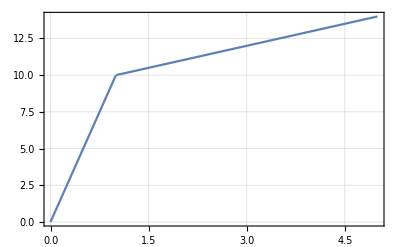

allContracts

(3 | 565 | {{2,80,10},{3,20,5}} | 113 | 0
1 | 752 | {{1,200,50},{2,80,10}} | 145 | 0
3 | 2789 | {{1,60,10},{2,100,25},{3,40,5}} | 111 | 0
2 | 999 | {{1,80,10},{2,400,100},{3,40,5},{4,30,5}} | 120 | 0
2 | 1585 | {{2,60,10},{3,1000,100}} | 135 | 0
1 | 527 | {{1,600,100},{3,100,25}} | 135 | 0)

allExchangeRates

(1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1)

allInterestRates

(97 | 10000
66 | 10000
52 | 10000
85 | 10000)

allAssets

(250
431
8441
8319)

Contract Cost

contr = {3,565,{{2,80,10},{3,20,5}},113,0}

descr = {{2,80,10},{3,20,5}}

payVal = {5,4}

cost = -46330

change = {0,-120,-35,0}

Variables

allVars

({x1V2,x1V3}
{x2V1,x2V2}
{x3V1,x3V2,x3V3}
{x4V1,x4V2,x4V3,x4V4}
{x5V2,x5V3}
{x6V1,x6V3})

allVarsLinear

{x1V2,x1V3,x2V1,x2V2,x3V1,x3V2,x3V3,x4V1,x4V2,x4V3,x4V4,x5V2,x5V3,x6V1,x6V3}

nonNegativeCond

x1V2≥0&&x1V3≥0&&x2V1≥0&&x2V2≥0&&x3V1≥0&&x3V2≥0&&x3V3≥0&&x4V1≥0&&x4V2≥0&&x4V3≥0&&x4V4≥0&&x5V2≥0&&x5V3≥0&&x6V1≥0&&x6V3≥0

generateContractCost

generateContractCost[1] = -113/2 (565+35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2+√((565+35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2+15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3)^2)+15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3)

generatePositionChange

{0,35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2,15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3,0}

generateMaxFunc

-113/2 (565+35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2+√((565+35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2+15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3)^2)+15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3)-145/2 (752+75 (-1+√((-1+x2V1)^2)-x2V1)-50 x2V1+√((752+75 (-1+√((-1+x2V1)^2)-x2V1)-50 x2V1+35 (-1+√((-1+x2V2)^2)-x2V2)-10 x2V2)^2)+35 (-1+√((-1+x2V2)^2)-x2V2)-10 x2V2)-111/2 (2789+25 (-1+√((-1+x3V1)^2)-x3V1)-10 x3V1+75/2 (-1+√((-1+x3V2)^2)-x3V2)-25 x3V2+√((2789+25 (-1+√((-1+x3V1)^2)-x3V1)-10 x3V1+75/2 (-1+√((-1+x3V2)^2)-x3V2)-25 x3V2+35/2 (-1+√((-1+x3V3)^2)-x3V3)-5 x3V3)^2)+35/2 (-1+√((-1+x3V3)^2)-x3V3)-5 x3V3)+85 (8319+25/2 (-1+√((-1+x4V4)^2)-x4V4)-5 x4V4)-60 (999+35 (-1+√((-1+x4V1)^2)-x4V1)-10 x4V1+150 (-1+√((-1+x4V2)^2)-x4V2)-100 x4V2+35/2 (-1+√((-1+x4V3)^2)-x4V3)-5 x4V3+√(999+35 (-1+√((-1+x4V1)^2)-x4V1)-10 x4V1+150 (-1+√((-1+x4V2)^2)-x4V2)-100 x4V2+35/2 (-1+√((-1+x4V3)^2)-x4V3)-5 x4V3+25/2 (-1+√((-1+x4V4)^2)-x4V4)-5 x4V4)^2+25/2 (-1+√((-1+x4V4)^2)-x4V4)-5 x4V4)+66 (431+35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2+35 (-1+√((-1+x2V2)^2)-x2V2)-10 x2V2+75/2 (-1+√((-1+x3V2)^2)-x3V2)-25 x3V2+150 (-1+√((-1+x4V2)^2)-x4V2)-100 x4V2+25 (-1+√((-1+x5V2)^2)-x5V2)-10 x5V2)-135/2 (1585+25 (-1+√((-1+x5V2)^2)-x5V2)-10 x5V2+√((1585+25 (-1+√((-1+x5V2)^2)-x5V2)-10 x5V2+450 (-1+√((-1+x5V3)^2)-x5V3)-100 x5V3)^2)+450 (-1+√((-1+x5V3)^2)-x5V3)-100 x5V3)+97 (250+75 (-1+√((-1+x2V1)^2)-x2V1)-50 x2V1+25 (-1+√((-1+x3V1)^2)-x3V1)-10 x3V1+35 (-1+√((-1+x4V1)^2)-x4V1)-10 x4V1+250 (-1+√((-1+x6V1)^2)-x6V1)-100 x6V1)+52 (8441+15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3+35/2 (-1+√((-1+x3V3)^2)-x3V3)-5 x3V3+35/2 (-1+√((-1+x4V3)^2)-x4V3)-5 x4V3+450 (-1+√((-1+x5V3)^2)-x5V3)-100 x5V3+75/2 (-1+√((-1+x6V3)^2)-x6V3)-25 x6V3)-135/2 (527+250 (-1+√((-1+x6V1)^2)-x6V1)-100 x6V1+√((527+250 (-1+√((-1+x6V1)^2)-x6V1)-100 x6V1+75/2 (-1+√((-1+x6V3)^2)-x6V3)-25 x6V3)^2)+75/2 (-1+√((-1+x6V3)^2)-x6V3)-25 x6V3)

nonNegativeCond

x1V2≥0&&x1V3≥0&&x2V1≥0&&x2V2≥0&&x3V1≥0&&x3V2≥0&&x3V3≥0&&x4V1≥0&&x4V2≥0&&x4V3≥0&&x4V4≥0&&x5V2≥0&&x5V3≥0&&x6V1≥0&&x6V3≥0

nonNegBalanceCond

250+75 (-1+√((-1+x2V1)^2)-x2V1)-50 x2V1+25 (-1+√((-1+x3V1)^2)-x3V1)-10 x3V1+35 (-1+√((-1+x4V1)^2)-x4V1)-10 x4V1+250 (-1+√((-1+x6V1)^2)-x6V1)-100 x6V1≥0&&431+35 (-1+√((-1+x1V2)^2)-x1V2)-10 x1V2+35 (-1+√((-1+x2V2)^2)-x2V2)-10 x2V2+75/2 (-1+√((-1+x3V2)^2)-x3V2)-25 x3V2+150 (-1+√((-1+x4V2)^2)-x4V2)-100 x4V2+25 (-1+√((-1+x5V2)^2)-x5V2)-10 x5V2≥0&&8441+15/2 (-1+√((-1+x1V3)^2)-x1V3)-5 x1V3+35/2 (-1+√((-1+x3V3)^2)-x3V3)-5 x3V3+35/2 (-1+√((-1+x4V3)^2)-x4V3)-5 x4V3+450 (-1+√((-1+x5V3)^2)-x5V3)-100 x5V3+75/2 (-1+√((-1+x6V3)^2)-x6V3)-25 x6V3≥0&&8319+25/2 (-1+√((-1+x4V4)^2)-x4V4)-5 x4V4≥0

Wed 22 Nov 2017 04:25:09, time used: 0.047, total time used: 0.
---------------------------------------------

Calling NMaximize...

Wed 22 Nov 2017 05:09:03, time used: 2635, total time used: 2635.
---------------------------------------------

sol = {798443.,{x1V2→0,x1V3→110,x2V1→2,x2V2→36,x3V1→0,x3V2→0,x3V3→551,x4V1→0,x4V2→0,x4V3→193,x4V4→0,x5V2→0,x5V3→7,x6V1→0,x6V3→18}}

```mathematica
(* ==============================================*)
ClearAll["Global`*"];
(* ==============================================*)
(* Set the same seedRandomValue for deterministic results *)
rndVal=RandomInteger[{0,10^12}];
seedRandomValue=rndVal;
seedRandomValue = 597543585369;
SeedRandom[seedRandomValue];
Print["seedRandomValue = ", seedRandomValue];
(* ==============================================*)
(* Parameters *)
noOfContracts =6;
noOfAssets = 4;

incrValues = {5,10,25,50,100};
minValMultipliers = {4,6,8,10};

(*
minRate = 0.01; (* Around JPY *)
maxRate = 3; (* Around KWD / BHD / OMR *)
*)

minRate = 1;
maxRate = 1;

(*
maxIncomeAnnualRate = 1.0 ;
maxBorrowingAnnualRate = 3.0 ;
maxNonPayingAnnualRate = 10.0 ;
*)

maxIncomeAnnualRate = 100 ;
(* maxBorrowingAnnualRate = 3.0 ; *)
maxNonPayingAnnualRate = 200 ;

maxContractAmount = 3000;

(* Adjust as necessary *)
(* min/max amount of assets before settlement *)
amountMultiplier = noOfContracts * maxContractAmount / 2;
minAmountOnHand = -(amountMultiplier/5)*0;
maxAmountOnHand = amountMultiplier;
(* ==============================================*)
minNoOfRes = Min[2, noOfAssets];
maxNoOfRes =  Min[10, noOfAssets];
baseAccountingAsset = 1; (* Asset in which perform all calculations. *)
(* ==============================================*)
(* Function to calculate payment amount for the contract *)
(* x - ID of payment: 0 - do not pay, 1 - pay minAmount (m), over 1 - pay minAmount + step * (x - 1) *)
fPay[x_, m_, s_]:=s*x-((m-s)*(-1+Sqrt[(-1+x)^2]-x))/2;
Print[Plot[fPay[x, 10,1],{x, 0,5}, PlotRange-> All, Frame->True, GridLines->Automatic]];
(* ==============================================*)
(* Some legacy stuff... *)
strSeparator = "=============================================" <> FromCharacterCode[10];
strSeparatorSmall = "---------------------------------------------";
strCRLF = FromCharacterCode[10];
tStart = AbsoluteTime[];
tMid = tStart;

printTimeUsed[showTime_?BooleanQ] := Module[{tEnd, now, diff, diffTot},
  tEnd = AbsoluteTime[];
  now = DateString[];

  If[showTime,
    (
      diff = tEnd - tMid;

      If[diff < 100,
        (
          diff = N[Round[diff, 10^-3]];
        ),
        (
          diff = Round[diff];
        )
      ];

      diffTot = Round[tEnd - tStart];
      Print[now, ", time used: ", diff, ", total time used: ", diffTot, ".", FromCharacterCode[10] <> strSeparatorSmall]
    ),
    (
      Print["Time used reset."]
    )
  ];

  tMid = tEnd;
];

printTimeUsed[] := printTimeUsed[True];
(* ==============================================*)
(* TODO: The distribution of exchange rates is clearly not uniform. This is irrelevant for the test. *)
(* TODO: Account for exchange rate spread if necessary *)
(* Exchange rates between assets. Modify as appropriate. *)
getExchangeRates[]:=Module[{retVal, rateToBase},
(* rateToBase=Table[If[ii==1, 1, RandomReal[{minRate, maxRate}]],{ii,1,noOfAssets}]; *)
rateToBase=Table[1,{ii,1,noOfAssets}];
retVal = Table[If[ii==jj, 1,rateToBase[[ii]]/rateToBase[[jj]]],{ii,1,noOfAssets},{jj,1,noOfAssets}];
Return[retVal];
];

(* Number of resources for a contract *)
getNoOfRes[]:=RandomInteger[{minNoOfRes, maxNoOfRes}];

(* Resources used by a contract*)
getResources[]:=Module[{noOfRes, retVal,len, noDupl},
noOfRes = getNoOfRes[];

(* Chances of NOT getting enough are small. It is irrelevant for this test. *)
noDupl = DeleteDuplicates[Table[RandomInteger[{1, maxNoOfRes}],{ii,1,noOfRes + 2}]];
retVal =Take[noDupl, Min[noOfRes, Length[noDupl]]];
Return[retVal];
];

(* TODO: Account for the exchange rate - weak currency should have larger increment *)
(* Increment for a contract *)
getIncrement[]:=incrValues[[RandomInteger[{1, Length[incrValues]}]]];

(* Min value for a contract *)
getMinValue[incr_]:=incr * minValMultipliers[[RandomInteger[{1, Length[minValMultipliers]}]]];

(* *)
(* TODO: Rounding rules were not specified *)
getResourceDescriptor[resource_]:=Module[{retVal, increment, minVal},
increment = getIncrement[];
minVal =getMinValue[increment];

retVal = {resource, minVal, increment};
Return[retVal];
];

(* Update as needed... *)
resourceDescriptorQ[rd_]:=If[VectorQ[rd] && Length[rd]== 3, True, False, False];

(* Do not want to use associations, datasets, ... *)
rdGetAsset[rd_?resourceDescriptorQ]:=rd[[1]];
rdGetMinVal[rd_?resourceDescriptorQ]:=rd[[2]];
rdGetIncr[rd_?resourceDescriptorQ]:=rd[[3]];

(* *)
getContract[]:=Module[{retVal, resoures, increment, minVal, amount,baseCurrency, nonPayingRate, overPayingRate},
resoures = getResources[];
baseCurrency=resoures[[RandomInteger[{1,Length[resoures]}]]];
amount=RandomInteger[maxContractAmount];
nonPayingRate = RandomInteger[{maxIncomeAnnualRate, maxNonPayingAnnualRate}];

(*  RandomReal[{maxBorrowingAnnualRate, maxNonPayingAnnualRate}] / 365 *)
overPayingRate=0; (* Update if needed *)

retVal = {baseCurrency,amount,SortBy[Table[getResourceDescriptor[resoures[[ii]]],{ii,1,Length[resoures]}], First], nonPayingRate, overPayingRate};
Return[retVal];
];

(* Update as needed... *)
contractQ[c_]:=If[ListQ[c]&& Length[c]==5,True,False, False];

contrGetBaseCurrency[c_?contractQ]:=c[[1]];
contrGetAmount[c_?contractQ]:=c[[2]];
contrGetDescr[c_?contractQ]:=c[[3]];
contrGetNonPayingRate[c_?contractQ]:=c[[4]];
contrGetOverPayingRate[c_?contractQ]:=c[[5]];

(* *)
getAllContracts[]:=Module[{retVal},
retVal = Table[getContract[],{ii,1,noOfContracts}];
Return[retVal];
];

(* Interest rates on positive / negative balances *)
getInstrumentInterestRate[]:=Module[{retVal, positiveRate, negativeRate},
(*
positiveRate =RandomReal[{0, maxIncomeAnnualRate}];
negativeRate = RandomReal[{positiveRate, maxBorrowingAnnualRate}];
*)
positiveRate =RandomInteger[{0, maxIncomeAnnualRate}];
negativeRate =10^4; (* Do not want to borrow... *)

retVal = {positiveRate, negativeRate} (* / 365 *);
Return[retVal];
];

getInterestRates[]:=Module[{retVal},
retVal=Table[getInstrumentInterestRate[],{ii, 1, noOfAssets}];
Return[retVal];
];

(* Update as needed... *)
interestRateQ[c_]:=If[ListQ[c]&& Length[c]==2,True,False, False];

intGetIncomeRate[d_?interestRateQ]:=d[[1]];
intGetBorrowingRate[d_?interestRateQ]:=d[[2]];

getAssets[]:=Module[{retVal},
retVal = Table[RandomInteger[{minAmountOnHand, maxAmountOnHand}],{ii,1,noOfAssets}];
Return[retVal];
];
(* ==============================================*)
(* Must be at the top if getIncrement and getMinValue have to be modified to account for the rates. *)
allExchangeRates = getExchangeRates[];

allContracts = getAllContracts[];
(* allWeights = getWeights[]; *)
allInterestRates = getInterestRates[];

allAssets = getAssets[];
(* ==============================================*)
getExchangeRate[from_?IntegerQ, to_?IntegerQ]:=allExchangeRates[[from, to]];
(* ==============================================*)
(* Amount in the base asset of the contract *)
getBaseAmount[amt_, deliveryAsset_?IntegerQ, baseAsset_?IntegerQ]:=Module[{retVal},
retVal = amt * getExchangeRate[deliveryAsset, baseAsset];
(* Print["getBaseAmount::retVal = ", retVal]; *)
Return[retVal];
];

(* valueID - ID of how much much to pay *)
(* Returns amount of the asset used for settlement *)
(* getDeliveryAmount[rd_?resourceDescriptorQ, valueID_?IntegerQ]:= *)
getDeliveryAmount[rd_?resourceDescriptorQ, valueID_]:=
Module[{retVal, res, minVal, incr},
res=rdGetAsset[rd];
 minVal=rdGetMinVal[rd];
incr =rdGetIncr[rd];
(* retVal=If[valueID>0, Evaluate[minVal + incr * (valueID - 1)], 0]; *)
retVal=fPay[valueID, minVal, incr];

(* Print["getDeliveryAmount::retVal = ", retVal]; *)
Return[retVal];
];

(* Cost of contract in accounting currency *)
(* v is vector of ... *)
getContractCost[contr_?contractQ, v_]:=Module[{retVal,len, baseAsset, amtToPay, descr, paid, netAmt, baseInc},
baseAsset = contrGetBaseCurrency[contr];
amtToPay = contrGetAmount[contr];
descr = contrGetDescr[contr];
(* Print["contrCost::descr = ", descr]; *)

len = Length [descr]; (* v must have the same length *)

(* Paid amount in base asset of the contract *)
paid=Sum[getBaseAmount[getDeliveryAmount[descr[[ii]], v[[ii]]], rdGetAsset[descr[[ii]]], baseAsset],{ii, 1, len}];

netAmt = amtToPay-paid;
(* baseInc = -netAmt*If[netAmt>0,  Evaluate[contrGetNonPayingRate[contr]],  Evaluate[contrGetOverPayingRate[contr]]]; *)
baseInc=-contrGetNonPayingRate[contr]*(Sqrt[netAmt^2]+netAmt)/2;

(* Amount in accounting currency *)
retVal=baseInc* getExchangeRate[baseAsset, baseAccountingAsset];
Return[retVal];
];

(* Calculate changes to position due to settlement of a given contract *)
getPositionChange[contr_?contractQ, v_]:=Module[{retVal, descr, len},
descr = contrGetDescr[contr];
len = Length [descr];
retVal=Table[0,{ii,1,noOfAssets}];

Do[
(
retVal[[ rdGetAsset[descr[[ii]]]]]-=getDeliveryAmount[descr[[ii]], v[[ii]]];
),
{ii,1,len}
];

Return[retVal];
];
(* ==============================================*)

Print["allContracts"];
allContracts // MatrixForm

Print["allExchangeRates"];
allExchangeRates // MatrixForm

Print["allInterestRates"];
allInterestRates // MatrixForm

Print["allAssets"];
allAssets // MatrixForm

Print["Contract Cost"];
contractID= 1;
contr = allContracts[[contractID]];
descr = contrGetDescr[contr];
payVal=Table[RandomInteger[{0,5}],{ii, 1, Length[descr]}];
cost=getContractCost[contr, payVal];
change = getPositionChange[contr, payVal];

Print["contr = ", contr];
Print["descr = ", descr];
Print["payVal = ", payVal];
Print["cost = ", cost];
Print["change = ", change];

(* ==============================================*)
Print["Variables"];
allVars=Table[ToExpression["x" <> ToString[ii] <> "V" <>  ToString[rdGetAsset[contrGetDescr[allContracts[[ii]]][[jj]]]]],{ii,1,noOfContracts}, {jj,1,Length[contrGetDescr[allContracts[[ii]]]]}];

allVarsLinear  = Flatten[allVars];

nonNegativeCond = "";
Do[nonNegativeCond = nonNegativeCond <> If[ii > 1, " && ", ""] <>ToString[allVarsLinear[[ii]]] <> " >= 0" ,{ii,1,Length[allVarsLinear]}];
nonNegativeCond=ToExpression[nonNegativeCond];

Print["allVars"];
Print[allVars // MatrixForm];
Print["allVarsLinear"];
Print[allVarsLinear];
Print["nonNegativeCond"];
Print[nonNegativeCond];

(* ==============================================*)
(* Maximization function *)
generateContractCost[contractID_?IntegerQ]:=Module[{retVal},
retVal=getContractCost[allContracts[[contractID]], allVars[[contractID]]];
(* Print["generateContractCost::retVal = ", retVal, "..."]; *)
Return[retVal];
];

generatePositionChange[contractID_?IntegerQ]:=Module[{retVal},
retVal=getPositionChange[allContracts[[contractID]], allVars[[contractID]]];

(* Print["generatePositionChange::retVal = ", retVal]; *)
Return[retVal];
];

generateBalance[]:=Module[{positionChange, balance},
positionChange=Sum[generatePositionChange[ii],{ii,1,noOfContracts}];
balance =allAssets + positionChange;
Return[balance];
];

generateMaxFunc[]:=Module[{retVal, cost, balance, assetIncome, totalAssetIncome},
cost=Sum[generateContractCost[ii],{ii,1,noOfContracts}];
balance=generateBalance[];

(*
assetIncome = Table[balance[[ii]]*If[balance[[ii]]≥0, Evaluate[intGetIncomeRate[allInterestRates[[ii]]]],Evaluate[intGetBorrowingRate[allInterestRates[[ii]]]]],{ii,1,noOfAssets}];
*)

assetIncome = Table[balance[[ii]]*intGetIncomeRate[allInterestRates[[ii]]],{ii,1,noOfAssets}];

totalAssetIncome = Sum[assetIncome[[ii]] * getExchangeRate[ii, baseAccountingAsset],{ii,1, noOfAssets}];
retVal=cost + totalAssetIncome;
(* Print["generateMaxFunc::retVal = ", retVal]; *)
Return[retVal];
];

allBalance=generateBalance[];
nonNegBalance=Table[allBalance[[ii]]≥ 0, {ii, 1, Length[allBalance]}];

nonNegBalanceCond = "";
Do[nonNegBalanceCond = nonNegBalanceCond <> If[ii > 1, " && ", ""] <>ToString[InputForm[allBalance[[ii]]]] <> " >= 0" ,{ii,1,Length[allBalance]}];
nonNegBalanceCond=ToExpression[nonNegBalanceCond];
(* ==============================================*)

Print["generateContractCost"];
Print["generateContractCost[1] = ", generateContractCost[1]]

Print["generatePositionChange"];
Print[generatePositionChange[1]]

Print["generateMaxFunc"];
maxFunc=generateMaxFunc[];
Print[maxFunc];

Print["nonNegativeCond"];
Print[nonNegativeCond];

Print["nonNegBalanceCond"];
Print[nonNegBalanceCond];


printTimeUsed[];
Print["Calling NMaximize..."];
sol = NMaximize[{maxFunc, nonNegativeCond && nonNegBalanceCond && Element[allVarsLinear, Integers]}, allVarsLinear, MaxIterations->100000];
printTimeUsed[];
Print["sol = ", sol];

(* ==============================================*)
```